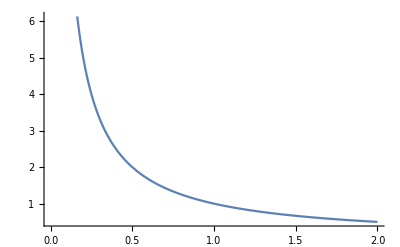

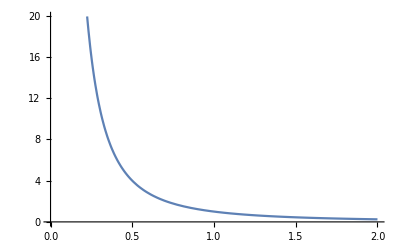

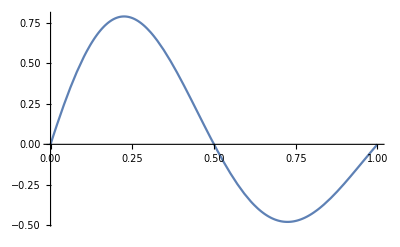

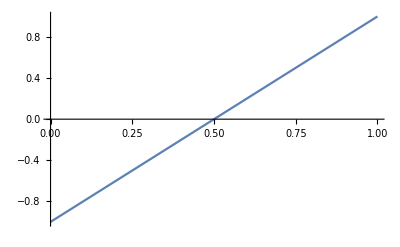

```mathematica
(*wolfram mathematica notebook*)
(*potential*)
ClearAll["Global`*"]
v1[d_,i_:2]:=1 / d^i;
Plot[v1[d,1], {d, 0, 2}]
Plot[v1[d,2], {d, 0, 2}]

v2[d_,dmax_:1]:=Sin[2 Pi d/dmax]Exp[-d/dmax];
v3[d_,dmax_:1]:=(2d-dmax)/dmax;
dmax:=1;
Plot[v2[d,dmax], {d, 0, dmax}]
Plot[v3[d,dmax], {d, 0, dmax}]
```

```mathematica
(* collision *)
ClearAll["Global`*"]
u1:=v1+f1/m1;
u2:=v2+f2/m2;
Solve[
{
m1 v1 + m2 v2 ==m1 u1+m2  u2,
m1 v1^2+m2 v2^2==m1 u1^2+m2 u2^2
},
{f1, f2}];
Factor[%]
```

{{f1→0,f2→0},{f1→-(2 m1 m2 (v1-v2))/(m1+m2),f2→(2 m1 m2 (v1-v2))/(m1+m2)}}

```mathematica
(* collision *)
ClearAll["Global`*"]
m1=1.;
x1={-1,0};
v1={1,0};

m2=1;
x2={1,0};
v2={-1,0};

s=2 m1 m2/(m1 + m2)
dx=x2-x1;
d2=(dx.dx);
dv=v2-v1;
f=s(dv.dx) dx/d2
v1f=v1+f/m1
x1f=x1+v1f
v2f=v2-f/m2;
x2f=x2+v2f;
```

1.

{-2.,0.}

{-1.,0.}

{-2.,0.}

```mathematica
(* potentials *)
ClearAll["Global`*"]
Manipulate[Plot[1/x^a, {x,0,1}], {a, 0, 3}]
Manipulate[Plot[Sin[2 Pi x a], {x,0,1}], {a, -2, 2, 0.5}]
Manipulate[Plot[Sin[2 Pi x]+a x^-2,{x,0,1}], {a, -1, 1}]
Manipulate[Plot[Sin[2Pi x]Exp[-a x], {x,0,1}, PlotRange->1], {a, 0, 2Pi}]
Manipulate[Plot[-Sin[2 Pi Exp[-(Log[2]/r)x] ],{x,0,1},PlotRange-> 1], {r, 0.01, 1}]
```

```mathematica
ClearAll["Global`*"]
v[x_,a_,b_]:=a (1- Exp[b x]);
Solve[{v[0,a,b]==0,v[1,a,b]==1},{a,b}];
ExpandAll[v[x,a,Log[(a-1)/a]]];
v2[x_,a_]:=a-(1-1/a)^x a;
Manipulate[Plot[v2[x,a],{x,0,1}],{a,1.001,3}]

f[x_,a_]:=Sin[2Pi v2[x,a]];
Manipulate[Plot[f[x,a],{x,0,1}],{a,1.001,3}]
ExpandAll[f[x,1.192]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Sin[7.48956-7.48956 0.161074^x]

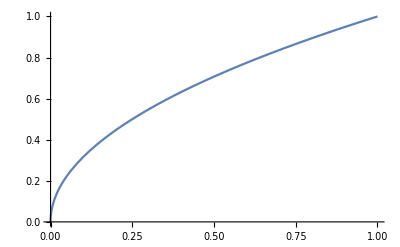

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{b→-Log[2]/Log[r]}}

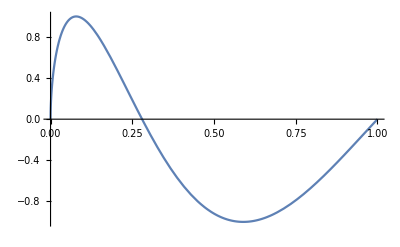

```mathematica
ClearAll["Global`*"]
v[x_,b_]:=x^b
f[x_,b_]:=Sin[2 Pi v[x,b]]
Plot[v[x,1/2],{x,0,1}]
Solve[v[r,b]==1/2,b]
a=1;
r=0.7/2.5;
b=-Log[2.0]/Log[r];
Plot[f[x,b],{x,0,1}]
```

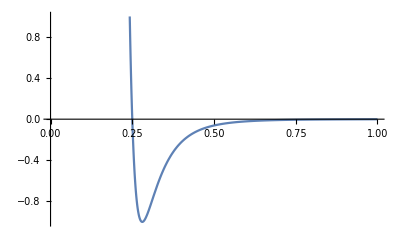

```mathematica
(* lennard jones potential*)
ClearAll["Global`*"]
v[r_,e_:1,a_:1]:=4e((a/r)^12-(a/r)^6)
Plot[v[4x],{x,0,1},PlotRange->1]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Sin[2 a π-a (2 π)^(1-x) (2 π-(2 π)/a)^x]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

{{0.1,0.000986237},{0.11,0.00186518},{0.12,0.00318361},{0.13,0.00502492},{0.14,0.00746186},{0.15,0.010557},{0.16,0.0143639},{0.17,0.0189296},{0.18,0.0242957},{0.19,0.0305005},{0.2,0.0375801},{0.21,0.0455703},{0.22,0.054507},{0.23,0.0644272},{0.24,0.0753703},{0.25,0.087378},{0.26,0.100496},{0.27,0.114773},{0.28,0.130262},{0.29,0.147024},{0.3,0.165122},{0.31,0.184627},{0.32,0.205619},{0.33,0.228182},{0.34,0.252411},{0.35,0.278412},{0.36,0.3063},{0.37,0.336202},{0.38,0.368259},{0.39,0.402628},{0.4,0.43948},{0.41,0.479008},{0.42,0.521425},{0.43,0.566967},{0.44,0.6159},{0.45,0.668518},{0.46,0.725152},{0.47,0.786173},{0.48,0.851998},{0.49,0.923097},{0.5,{}}}

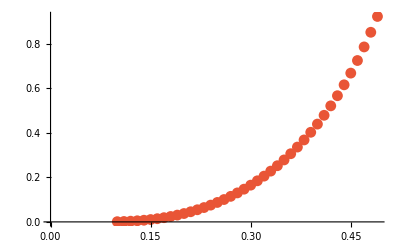

```mathematica
ClearAll["Global`*"]
v[x_,a_,b_]:=Sin[2 Pi a(1 - b^x)]
Manipulate[Plot[v[x,a,b],{x,0,1}],{a,0.01,2},{b,0.01,1}];

Solve[{v[0,a,b]==0,v[1,a,b]==0},{a,b}];
Manipulate[Plot[v[x,a,(2 a π+2 π C1)/(2 a π)],{x,0,1}],{a,-2,2},{C1,-5,5,1}];
Manipulate[Plot[v[x,a,(π+2 a π+2 π C1)/(2 a π)],{x,0,1}],{a,-2,2},{C1,-5,5,1}];
v2[x_,a_]:=v[x,a,(2 a π+2 π (-1))/(2 a π)]
ExpandAll[v2[x,a]]
Manipulate[Plot[v2[x,a],{x,0,1}],{a,1.001,3}];
v3[x_,a_]:=Sin[2 a π(1-(1-1/a)^x )]
Manipulate[Plot[v3[x,a],{x,0,1},PlotRange->1],{a,1.001,2}];
v4[x_,k_]:=Sin[2Pi/(1-k) (1-k^x)]
Manipulate[Plot[v4[x,k],{x,0,1},PlotRange->1],{k,0.001,0.999}];
table=Table[{r,NSolve[v4[r,k]==0&&0<k<1,k,Reals]},{r,0.1,0.5,0.01}];
list=table/.{{Rule[a_,b_]}} :> b
ListPlot[list]
```

```mathematica
v4[x,0.1302622971922101]
```

Sin[7.22423 (1-0.130262^x)]